# xPand Benchmarking

## Set up

```mathematica
SetDirectory["~/XPAND"];
```

```mathematica
Block[{Print},
<<xAct/xPand.m;
]
$DefInfoQ=False;
SetOptions[AutomaticRules,Verbose->False];
```

We define the manifold, the metric and the slicing

```mathematica
(*DefConstantSymbol[d];*)
DefManifold[M,4(*d*),{α,β,γ,μ,ν,λ,σ}];
DefMetric[-1,g[-α,-β],CD,{";","OverBar[∇]"},PrintAs->"ḡ"];
SetSlicing[hM,nM,g,cdM,{"|","D̄"},Minkowski];
SetSlicing[h,n,g,cd,{"|","D̄"},FLFlat];
SetSlicing[h2,n2,g,cd2,{"|","D̄"},FLCurved];
SetSlicing[h3,n3,g,cd3,{"|","D̄"},BianchiI];
SetSlicing[h4,n4,g,cd4,{"|","D̄"},BianchiB];
```

** DefMetric: Don't know yet how to define epsilon for a frozen metric.

** MakeRule: Potential problems moving indices on the LHS.

** DefMetric: Don't know yet how to define epsilon for a frozen metric.

** MakeRule: Potential problems moving indices on the LHS.

** DefMetric: Don't know yet how to define epsilon for a frozen metric.

** MakeRule: Potential problems moving indices on the LHS.

** DefMetric: Don't know yet how to define epsilon for a frozen metric.

** MakeRule: Potential problems moving indices on the LHS.

These commands are necessary, but if they are forgotten, they are automatically called. So for a minimal example we do not evaluate them

```mathematica
DefMetricFields[g,dg,hM]
DefMatterFields[uf, duf,hM]

DefMetricFields[g,dg,h]
DefMatterFields[uf, duf,h]

DefMetricFields[g,dg,h2]
DefMatterFields[uf, duf,h2]

DefMetricFields[g,dg,h3]
DefMatterFields[uf, duf,h3]

DefMetricFields[g,dg,h4]
DefMatterFields[uf, duf,h4]
```

The Hubble factor  has to be introduced from the scale factor.

## Benchmark

```mathematica
MyxPandBenchMark[expr_,h_,order_,gauge_]:=ToxPand[expr,dg,uf,duf,h, gauge, order]
```

```mathematica
ordermax=4
```

4

```mathematica
$OpenConstantsOfStructure=False;
```

```mathematica
TimingsxPert=Table[{i,First@AbsoluteTiming[ExpandPerturbation@Perturbed[Conformal[g,gah42][RicciScalarCD[]],i]//ContractMetric//ToCanonical]},{i,1,ordermax+1}]
```

{{1,0.16322},{2,0.568025},{3,2.45161},{4,13.68355},{5,154.18833}}

```mathematica
TimingsMinkowski=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],hM,i,NewtonGauge]]},{i,1,ordermax}]
TimingsMinkowskiSynchronous=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],hM,i,SynchronousGauge]]},{i,1,ordermax}]
TimingsMinkowskiFlat=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],hM,i,FlatGauge]]},{i,1,ordermax}]
TimingsMinkowskiComoving=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],hM,i,ComovingGauge]]},{i,1,ordermax}]
TimingsMinkowskiAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],hM,i,AnyGauge]]},{i,1,ordermax}]
```

$Aborted

$Aborted

$Aborted

«2 more identical outputs»

```mathematica
TimingsFLFlat=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h,i,NewtonGauge]]},{i,1,ordermax}]
TimingsFLFlatSynchronous=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h,i,SynchronousGauge]]},{i,1,ordermax}]
TimingsFLFlatFlat=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h,i,FlatGauge]]},{i,1,ordermax}]
TimingsFLFlatComoving=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h,i,ComovingGauge]]},{i,1,ordermax}]
TimingsFLFlatAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h,i,AnyGauge]]},{i,1,ordermax}]
```

{{1,1.77504},{2,11.13674},{3,91.07043}}

{{1,1.98621},{2,17.93648},{3,181.87755}}

{{1,1.75934},{2,10.30359},{3,92.26664}}

{{1,1.89883},{2,11.81138},{3,102.89702}}

{{1,2.18146},{2,24.10119},{3,297.02536}}

```mathematica
TimingsFLCurved=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h2,i,NewtonGauge]]},{i,1,ordermax}]
TimingsFLCurvedSynchronous=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h2,i,SynchronousGauge]]},{i,1,ordermax}]
TimingsFLCurvedFlat=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h2,i,FlatGauge]]},{i,1,ordermax}]
TimingsFLCurvedComoving=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h2,i,ComovingGauge]]},{i,1,ordermax}]
TimingsFLCurvedAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h2,i,AnyGauge]]},{i,1,ordermax-1}]
```

{{1,1.84103},{2,10.0521},{3,90.74164}}

{{1,2.07749},{2,22.0454},{3,252.51494}}

{{1,1.78962},{2,11.17143},{3,97.226583}}

{{1,1.99694},{2,13.20699},{3,115.33069}}

{{1,2.3973},{2,32.08256}}

```mathematica
TimingsBianchiI=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h3,i,NewtonGauge]]},{i,1,ordermax}]
TimingsBianchiISynchronous=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h3,i,SynchronousGauge]]},{i,1,ordermax}]
TimingsBianchiIFlat=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h3,i,FlatGauge]]},{i,1,ordermax}]
TimingsBianchiIComoving=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h3,i,ComovingGauge]]},{i,1,ordermax}]
TimingsBianchiIAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h3,i,AnyGauge]]},{i,1,ordermax-1}]
```

{{1,5.33672},{2,34.71568},{3,660.11928}}

{{1,6.3242},{2,57.72988},{3,924.01101}}

{{1,4.73366},{2,28.3648},{3,643.61748}}

{{1,5.25914},{2,37.78746},{3,724.80684}}

{{1,6.26068},{2,67.83596}}

```mathematica
TimingsBianchiB=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h4,i,NewtonGauge]]},{i,1,ordermax-1}]
TimingsBianchiBSynchronous=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h4,i,SynchronousGauge]]},{i,1,ordermax-1}]
TimingsBianchiBFlat=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h4,i,FlatGauge]]},{i,1,ordermax-1}]
TimingsBianchiBComoving=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h4,i,ComovingGauge]]},{i,1,ordermax-1}]
TimingsBianchiBAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h4,i,AnyGauge]]},{i,1,ordermax-2}]
```

{{1,12.27651},{2,89.02699}}

{{1,18.79393},{2,418.99102}}

{{1,9.38567},{2,54.03946}}

{{1,12.77371},{2,101.87227}}

{{1,19.89411}}

## Saving results and Plots

Just to have an idea of the ratio of timings between succesive orders. We clearly see that it is an approximate power law.

```mathematica
FirstTime=True
```

True

```mathematica
NameFileNewt=StringJoin["SaveTimingsNewtonGauge",ToString[ordermax],".dat"];
If[FirstTime,
Put[{TimingsxPert,TimingsMinkowski,TimingsFLFlat,TimingsFLCurved,TimingsBianchiI,TimingsBianchiB},NameFileNewt];,{TimingsxPert,TimingsMinkowski,TimingsFLFlat,TimingsFLCurved,TimingsBianchiI,TimingsBianchiB}=Get[NameFileNewt]]


NameFileSynchronous=StringJoin["SaveTimingsSynchronousGauge",ToString[ordermax],".dat"];
If[FirstTime,
Put[{TimingsxPert,TimingsMinkowskiSynchronous,TimingsFLFlatSynchronous,TimingsFLCurvedSynchronous,TimingsBianchiISynchronous,TimingsBianchiBSynchronous},NameFileSynchronous];,{TimingsxPert,TimingsMinkowskiSynchronous,TimingsFLFlatSynchronous,TimingsFLCurvedSynchronous,TimingsBianchiISynchronous,TimingsBianchiBSynchronous}=Get[NameFileSynchronous]]

NameFileFlat=StringJoin["SaveTimingsFlatGauge",ToString[ordermax],".dat"];
If[FirstTime,
Put[{TimingsxPert,TimingsMinkowskiFlat,TimingsFLFlatFlat,TimingsFLCurvedFlat,TimingsBianchiIFlat,TimingsBianchiBFlat},NameFileFlat];,{TimingsxPert,TimingsMinkowskiFlat,TimingsFLFlatFlat,TimingsFLCurvedFlat,TimingsBianchiIFlat,TimingsBianchiBFlat}=Get[NameFileFlat]]


NameFileComoving=StringJoin["SaveTimingsComovingGauge",ToString[ordermax],".dat"];
If[FirstTime,
Put[{TimingsxPert,TimingsMinkowskiComoving,TimingsFLFlatComoving,TimingsFLCurvedComoving,TimingsBianchiIComoving,TimingsBianchiBComoving},NameFileComoving];,{TimingsxPert,TimingsMinkowskiComoving,TimingsFLFlatComoving,TimingsFLCurvedComoving,TimingsBianchiIComoving,TimingsBianchiBComoving}=Get[NameFileComoving]]
```

```mathematica
NameFileAny=StringJoin["SaveTimingsAnyGauge",ToString[ordermax],".dat"];
If[FirstTime,
Put[{TimingsxPert,TimingsMinkowskiAny,TimingsFLFlatAny,TimingsFLCurvedAny,TimingsBianchiIAny,TimingsBianchiBAny},NameFileAny];,{TimingsxPert,TimingsMinkowskiAny,TimingsFLFlatAny,TimingsFLCurvedAny,TimingsBianchiIAny,TimingsBianchiBAny}=Get[NameFileAny]]
```

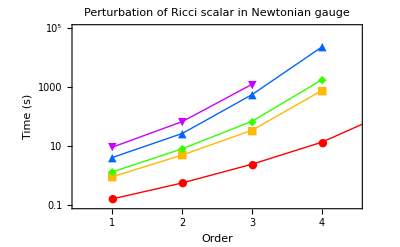

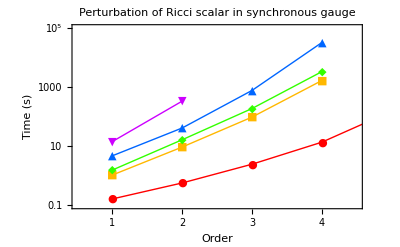

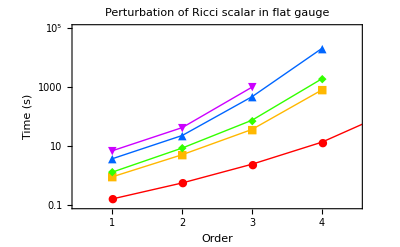

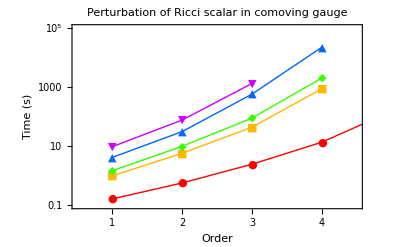

```mathematica
plotnewt=ListLogPlot[{TimingsxPert,TimingsMinkowski,(*TimingsFLFlat,*)TimingsFLCurved,TimingsBianchiI,TimingsBianchiB},Frame->True,FrameLabel->{Style["Order",12],Style["Time (s)",12]},PlotRange->{{0.5,ordermax+0.5},{.1,100000}},PlotLabel->Style["Perturbation of Ricci scalar in Newtonian gauge",12],PlotMarkers->{Automatic,Medium},FrameStyle->{{Thickness[.0035],Thickness[.0035]},{Thickness[.0035],Thickness[.0035]}},Joined->True,PlotStyle->{Hue[0],Hue[0.12],Hue[0.3],Hue[0.6],Hue[0.8],Hue[0.9]}]

plotsync=ListLogPlot[{TimingsxPert,TimingsMinkowskiSynchronous,(*TimingsFLFlat,*)TimingsFLCurvedSynchronous,TimingsBianchiISynchronous,TimingsBianchiBSynchronous},Frame->True,FrameLabel->{Style["Order",12],Style["Time (s)",12]},PlotRange->{{0.5,ordermax+0.5},{.1,100000}},PlotLabel->Style["Perturbation of Ricci scalar in synchronous gauge",12],PlotMarkers->{Automatic,Medium},FrameStyle->{{Thickness[.0035],Thickness[.0035]},{Thickness[.0035],Thickness[.0035]}},Joined->True,PlotStyle->{Hue[0],Hue[0.12],Hue[0.3],Hue[0.6],Hue[0.8],Hue[0.9]}]

plotflat=ListLogPlot[{TimingsxPert,TimingsMinkowskiFlat,(*TimingsFLFlat,*)TimingsFLCurvedFlat,TimingsBianchiIFlat,TimingsBianchiBFlat},Frame->True,FrameLabel->{Style["Order",12],Style["Time (s)",12]},PlotRange->{{0.5,ordermax+0.5},{.1,100000}},PlotLabel->Style["Perturbation of Ricci scalar in flat gauge",12],PlotMarkers->{Automatic,Medium},FrameStyle->{{Thickness[.0035],Thickness[.0035]},{Thickness[.0035],Thickness[.0035]}},Joined->True,PlotStyle->{Hue[0],Hue[0.12],Hue[0.3],Hue[0.6],Hue[0.8],Hue[0.9]}]

plotcom=ListLogPlot[{TimingsxPert,TimingsMinkowskiComoving,(*TimingsFLFlat,*)TimingsFLCurvedComoving,TimingsBianchiIComoving,TimingsBianchiBComoving},Frame->True,FrameLabel->{Style["Order",12],Style["Time (s)",12]},PlotRange->{{0.5,ordermax+0.5},{.1,100000}},PlotLabel->Style["Perturbation of Ricci scalar in comoving gauge",12],PlotMarkers->{Automatic,Medium},FrameStyle->{{Thickness[.0035],Thickness[.0035]},{Thickness[.0035],Thickness[.0035]}},Joined->True,PlotStyle->{Hue[0],Hue[0.12],Hue[0.3],Hue[0.6],Hue[0.8],Hue[0.9]}]
```

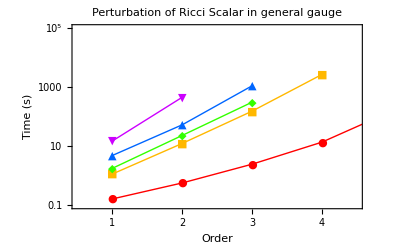

```mathematica
plotany=ListLogPlot[{TimingsxPert,TimingsMinkowskiAny,(*TimingsFLFlatAny,*)TimingsFLCurvedAny,TimingsBianchiIAny,TimingsBianchiBAny},Frame->True,FrameLabel->{Style["Order",12],Style["Time (s)",12]},PlotRange->{{0.5,ordermax+0.5},{.1,100000}},PlotLabel->Style["Perturbation of Ricci Scalar in general gauge",12],PlotMarkers->{Automatic,Medium},FrameStyle->{{Thickness[.0035],Thickness[.0035]},{Thickness[.0035],Thickness[.0035]}},Joined->True,PlotStyle->{Hue[0],Hue[0.12],Hue[0.3],Hue[0.6],Hue[0.8]}]
```

```mathematica
Export["TimingNewtonGauge.pdf",plotnewt,"pdf"];
Export["TimingNewtonGauge.eps",plotnewt,"eps"];

Export["TimingSynchronousGauge.pdf",plotsync,"pdf"];
Export["TimingSynchronousGauge.eps",plotsync,"eps"];

Export["TimingFlatGauge.pdf",plotflat,"pdf"];
Export["TimingFlatGauge.eps",plotflat,"eps"];

Export["TimingComovingGauge.pdf",plotcom,"pdf"];
Export["TimingComovingGauge.eps",plotcom,"eps"];
```

```mathematica
Export["TimingAnyGauge.pdf",plotany,"pdf"];
Export["TimingAnyGauge.eps",plotany,"eps"];
```